```mathematica
normalizedBgCorrectedGFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,50 ]
]
];
```

```mathematica
normalizedBgCorrectedRFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,39 ]
]
];
```

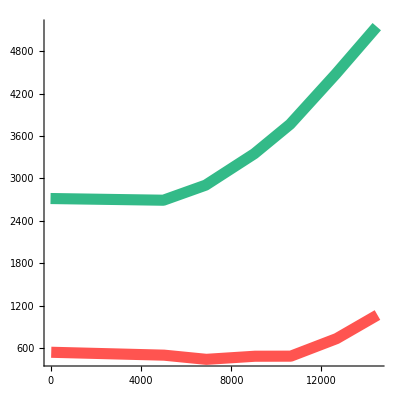

```mathematica
generateCombinedPlotOfColumn[gfpData, rfpData, 6]
```

```mathematica
makePdfGfpRfp[normalizedBgCorrectedGFP, normalizedBgCorrectedRFP, 8, 12]
```

myPlot.pdf

```mathematica
rfpData//MatrixForm
```

```mathematica
DevideElementWise[rfpData, odData]//MatrixForm
```

(Time | T° | mCh578 | mch614 | A1 | A2 | A3 | A4 | A5 | A6 | A7 | A8 | A9 | A10 | A11 | A12 | B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | C1 | C2 | C3 | C4 | C5 | C6 | C7 | C8 | C9 | C10 | C11 | C12 | D1 | D2 | D3 | D4 | D5 | D6 | D7 | D8 | D9 | D10 | D11 | D12 | E1 | E2 | E3 | E4 | E5 | E6 | E7 | E8 | E9 | E10 | E11 | E12 | F1 | F2 | F3 | F4 | F5 | F6 | F7 | F8 | F9 | F10 | F11 | F12 | G1 | G2 | G3 | G4 | G5 | G6 | G7 | G8 | G9 | G10 | G11 | G12 | H1 | H2 | H3 | H4 | H5 | H6 | H7 | H8 | H9 | H10 | H11 | H12
0:00:31 | 29.6 | 338 | 407 | 7921.57 | 10920. | 10072.7 | 7826.92 | 7403.85 | 7000. | 8220. | 11894.7 | 12447.4 | 10025.6 | 9263.16 | 7352.94 | 7333.33 | 9321.43 | 10823.5 | 8176.47 | 7176.47 | 9039.22 | 8705.88 | 8192.31 | 8326.92 | 6882.35 | 8294.12 | 11106.4 | 7104.17 | 7979.17 | 7076.92 | 8916.67 | 8708.33 | 6562.5 | 9829.79 | 10520.8 | 8687.5 | 8020.83 | 10791.7 | 8895.83 | 8959.18 | 9660. | 9276.6 | 10354.2 | 7468.09 | 9666.67 | 33187.5 | 41708.3 | 35795.9 | 36270.8 | 7122.45 | 4559.32 | 8923.08 | 7627.45 | 6254.9 | 8384.62 | 7653.85 | 6923.08 | 10411.8 | 8319.15 | 8489.36 | 24541.7 | 7395.83 | 8294.12 | 8058.82 | 7823.53 | 7568.63 | 13960.8 | 6689.66 | 9294.12 | 6942.31 | 7791.67 | 7458.33 | 8916.67 | 41085.1 | 38375. | 33375. | 41791.7 | 31916.7 | 39530.6 | 34895.8 | 40729.2 | 7979.59 | 8770.83 | 6166.67 | 8893.62 | 43106.4 | 39416.7 | 32936.2 | 35541.7 | 30148.9 | 41854.2 | 36142.9 | 36250. | 9895.83 | 6937.5 | 7382.98 | 7702.13 | 0. | 0
1:23:50 | 37. | 383 | 417 | 5969.23 | 7769.23 | 7029.41 | 6681.82 | 6014.93 | 6369.23 | 6656.25 | 11263.2 | 9923.08 | 11256.4 | 10948.7 | 7184.62 | 5500. | 5787.88 | 4955.22 | 5707.69 | 5712.12 | 7078.13 | 7634.92 | 7444.44 | 7107.69 | 5571.43 | 5046.88 | 7803.92 | 5730.77 | 7490.91 | 6803.57 | 6134.62 | 7400. | 5923.08 | 6470.59 | 7882.35 | 8923.08 | 8057.69 | 7764.71 | 6000. | 8264.15 | 9236.36 | 7176.47 | 8557.69 | 7040. | 7803.92 | 25865.4 | 27211.5 | 26075.5 | 27230.8 | 7961.54 | 3726.03 | 6515.15 | 5060.61 | 6671.88 | 6220.59 | 7415.38 | 5772.73 | 5390.63 | 7446.81 | 6404.26 | 6833.33 | 7666.67 | 4430.77 | 6718.75 | 6196.97 | 6151.52 | 8090.91 | 4791.67 | 5560.61 | 5692.31 | 8265.31 | 6270.83 | 6291.67 | 32425.5 | 27176.5 | 25423.1 | 27826.9 | 24509.8 | 25471.7 | 23403.8 | 22826.9 | 5433.96 | 9750. | 8020. | 7854.17 | 29106.4 | 24470.6 | 25078.4 | 24423.1 | 26784.3 | 26692.3 | 23641.5 | 25961.5 | 6153.85 | 7729.17 | 5659.57 | 8936.17 | 0. | 0
1:55:01 | 37. | 434 | 429 | 4362.5 | 5717.95 | 7329.41 | 3469.14 | 5156.63 | 5589.74 | 4923.08 | 10000. | 9897.44 | 11384.6 | 9102.56 | 4865.85 | 5209.88 | 5024.69 | 4333.33 | 6620.25 | 4353.66 | 3936.71 | 5551.28 | 3480.52 | 4531.65 | 4653.85 | 6141.03 | 6898.31 | 7763.64 | 7666.67 | 6035.71 | 8666.67 | 8423.08 | 7666.67 | 7384.62 | 8226.42 | 9055.56 | 7777.78 | 9188.68 | 6350. | 5305.08 | 6807.02 | 7018.87 | 7472.73 | 8627.45 | 8566.04 | 25092.6 | 21636.4 | 21184.6 | 22781.8 | 4733.33 | 4867.47 | 3445.78 | 4097.56 | 5012.2 | 5238.1 | 4658.54 | 3902.44 | 4550. | 6583.33 | 4125. | 6520.83 | 8333.33 | 4433.73 | 4382.72 | 5195.12 | 4048.19 | 5543.21 | 4234.69 | 4590.36 | 4575. | 5721.31 | 7708.33 | 6645.83 | 29787.2 | 26339.6 | 22290.9 | 22563.6 | 25773.6 | 23785.7 | 25000. | 22929.8 | 5581.82 | 7687.5 | 6653.06 | 6106.38 | 29458.3 | 26037.7 | 23264.2 | 26672.7 | 24923.1 | 26454.5 | 27555.6 | 22333.3 | 5924.53 | 11416.7 | 5653.06 | 6541.67 | 0. | 0
2:30:57 | 37. | 246 | 361 | 3242.99 | 4711.54 | 5116.07 | 3467.29 | 3378.38 | 3019.61 | 4087.38 | 13153.8 | 8615.38 | 9769.23 | 10282.1 | 3300. | 3121.5 | 3620.37 | 3621.36 | 3943.93 | 2834.86 | 4019.61 | 3297.03 | 3610. | 4782.18 | 3297.03 | 3872.55 | 8259.26 | 9596.49 | 6216.67 | 9719.3 | 5709.09 | 6754.72 | 10527.3 | 8377.36 | 8327.27 | 5927.27 | 6600. | 7037.74 | 7533.33 | 7896.55 | 7534.48 | 8962.96 | 8125. | 10307.7 | 9481.48 | 25581.8 | 23052.6 | 17522.4 | 23263.2 | 6016.39 | 2441.44 | 3073.39 | 3336.45 | 2318.18 | 2765.77 | 4157.41 | 3140.19 | 3028.3 | 7187.5 | 6395.83 | 5562.5 | 7625. | 3318.18 | 3824.07 | 3611.11 | 3092.59 | 4422.02 | 2336. | 3330.28 | 3721.15 | 7770.49 | 8083.33 | 7187.5 | 29702.1 | 21963.6 | 23160.7 | 22120.7 | 22944.4 | 23982.5 | 22614. | 18637.9 | 6821.43 | 8163.27 | 9000. | 6446.81 | 28916.7 | 25685.2 | 20037. | 24642.9 | 23264.2 | 21910.7 | 21563.6 | 22818.2 | 6555.56 | 17604.2 | 6945.45 | 5833.33 | 0. | 0
2:57:22 | 37. | 360 | 336 | 1992.7 | 3664.18 | 3312.5 | 3423.36 | 3248.23 | 2770.99 | 2590.91 | 9897.44 | 10307.7 | 10975. | 8589.74 | 3195.8 | 3323.53 | 2160.58 | 3147.06 | 2595.59 | 2364.29 | 2519.08 | 3960. | 3728. | 4267.72 | 2738.1 | 2515.63 | 10074.1 | 7071.43 | 7983.05 | 8927.27 | 9345.45 | 9716.98 | 10145.5 | 8396.23 | 6185.19 | 6833.33 | 6685.19 | 7037.74 | 8125. | 7237.29 | 8543.86 | 9711.54 | 8290.91 | 9980.77 | 9603.77 | 23592.6 | 23890.9 | 16757.6 | 25142.9 | 6540.98 | 2237.76 | 2438.85 | 3147.06 | 2253.52 | 2397.16 | 2147.89 | 3430.66 | 2160.31 | 6979.17 | 7125. | 8020.83 | 7229.17 | 2364.29 | 2131.39 | 2226.28 | 2695.65 | 3737.23 | 1787.1 | 2518.25 | 3610.69 | 7420. | 6921.57 | 8125. | 24383. | 20345.5 | 17214.3 | 21375. | 17943.4 | 19589.3 | 15403.2 | 16206.9 | 7145.45 | 8041.67 | 7551.02 | 5531.91 | 32770.8 | 22090.9 | 21240.7 | 21333.3 | 24444.4 | 18964.9 | 18833.3 | 18036.4 | 6792.45 | 7458.33 | 7480. | 6333.33 | 0. | 0
3:31:09 | 37. | 507 | 472 | 2228.72 | 4151.69 | 2551.89 | 2375. | 2217.62 | 2703.91 | 2494.44 | 11333.3 | 11044.4 | 8975. | 11333.3 | 2052.91 | 1575.27 | 1557.38 | 2276.92 | 2219.78 | 1818.65 | 2080. | 2397.59 | 2151.52 | 3578.31 | 3036.14 | 1894.74 | 7109.09 | 8446.43 | 6881.36 | 10323.1 | 9327.27 | 9452.83 | 11696.4 | 6056.6 | 7240.74 | 6703.7 | 7563.64 | 7603.77 | 7315.79 | 7129.03 | 9298.25 | 13660.4 | 9857.14 | 10717. | 10203.7 | 24727.3 | 29087.7 | 22686.6 | 25614. | 6828.13 | 2328.28 | 2264.55 | 1727.78 | 2107.69 | 2729.73 | 1867.35 | 2427.03 | 2554.29 | 8666.67 | 7125. | 6000. | 9020.83 | 1842.93 | 1497.3 | 2745.86 | 2271.28 | 2430.17 | 1723.08 | 2206.52 | 1621.47 | 7440. | 14254.9 | 5057.69 | 36666.7 | 27193. | 19807. | 28350.9 | 20981.8 | 18844.8 | 16343.8 | 17189.7 | 6836.36 | 6833.33 | 7714.29 | 7382.98 | 36367.3 | 43793.1 | 33873. | 48359.4 | 25312.5 | 19921.9 | 27736.8 | 20035.1 | 6537.04 | 8500. | 5134.62 | 7166.67 | 0. | 0
4:01:19 | 37. | 437 | 532 | 2265.82 | 4850.68 | 2010.95 | 2462.22 | 2358.41 | 2862.83 | 1325.99 | 8800. | 8645.83 | 11475. | 13307.7 | 1991.15 | 1434.04 | 2568.81 | 1810.08 | 2593.61 | 1828.57 | 1804.44 | 1865.38 | 2038.65 | 2815.53 | 2805.83 | 1449.54 | 5892.86 | 10362.1 | 9000. | 13029.4 | 10228.1 | 11436.4 | 10473.7 | 6870.37 | 4636.36 | 7309.09 | 6236.36 | 7074.07 | 5862.07 | 10258.1 | 7451.61 | 14063.5 | 7626.87 | 11163.6 | 13563.6 | 36160.7 | 31733.3 | 23842.9 | 42500. | 7188.41 | 2201.61 | 1898.31 | 2761.47 | 1710.94 | 2304.55 | 1934.11 | 2080.97 | 1504.42 | 6437.5 | 7312.5 | 8300. | 10795.9 | 1986.78 | 2978.17 | 2389.91 | 1962.96 | 3420.56 | 2051.59 | 2309.62 | 1711.86 | 6647.06 | 9000. | 7380. | 60860. | 31180.3 | 26557.4 | 51683.3 | 20387.1 | 25029.9 | 28616.7 | 25984.6 | 5216.67 | 6520.83 | 8081.63 | 8734.69 | 63687.5 | 40312.5 | 29650.8 | 44640.6 | 23307.7 | 36107.7 | 23697. | 19576.3 | 6981.13 | 14312.5 | 7148.15 | 7041.67 | 0. | 0)

```mathematica
rfpData//MatrixForm
```

(Time | T° | mCh578 | mch614 | A1 | A2 | A3 | A4 | A5 | A6 | A7 | A8 | A9 | A10 | A11 | A12 | B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | C1 | C2 | C3 | C4 | C5 | C6 | C7 | C8 | C9 | C10 | C11 | C12 | D1 | D2 | D3 | D4 | D5 | D6 | D7 | D8 | D9 | D10 | D11 | D12 | E1 | E2 | E3 | E4 | E5 | E6 | E7 | E8 | E9 | E10 | E11 | E12 | F1 | F2 | F3 | F4 | F5 | F6 | F7 | F8 | F9 | F10 | F11 | F12 | G1 | G2 | G3 | G4 | G5 | G6 | G7 | G8 | G9 | G10 | G11 | G12 | H1 | H2 | H3 | H4 | H5 | H6 | H7 | H8 | H9 | H10 | H11 | H12
0:00:31 | 29.6 | 338 | 407 | 404 | 546 | 554 | 407 | 385 | 357 | 411 | 452 | 473 | 391 | 352 | 375 | 374 | 522 | 552 | 417 | 366 | 461 | 444 | 426 | 433 | 351 | 423 | 522 | 341 | 383 | 368 | 428 | 418 | 315 | 462 | 505 | 417 | 385 | 518 | 427 | 439 | 483 | 436 | 497 | 351 | 464 | 1593 | 2002 | 1754 | 1741 | 349 | 269 | 464 | 389 | 319 | 436 | 398 | 360 | 531 | 391 | 399 | 1178 | 355 | 423 | 411 | 399 | 386 | 712 | 388 | 474 | 361 | 374 | 358 | 428 | 1931 | 1842 | 1602 | 2006 | 1532 | 1937 | 1675 | 1955 | 391 | 421 | 296 | 418 | 2026 | 1892 | 1548 | 1706 | 1417 | 2009 | 1771 | 1740 | 475 | 333 | 347 | 362 | 0 | 0
1:23:50 | 37. | 383 | 417 | 388 | 505 | 478 | 441 | 403 | 414 | 426 | 428 | 387 | 439 | 427 | 467 | 363 | 382 | 332 | 371 | 377 | 453 | 481 | 469 | 462 | 351 | 323 | 398 | 298 | 412 | 381 | 319 | 370 | 308 | 330 | 402 | 464 | 419 | 396 | 312 | 438 | 508 | 366 | 445 | 352 | 398 | 1345 | 1415 | 1382 | 1416 | 414 | 272 | 430 | 334 | 427 | 423 | 482 | 381 | 345 | 350 | 301 | 328 | 368 | 288 | 430 | 409 | 406 | 534 | 345 | 367 | 370 | 405 | 301 | 302 | 1524 | 1386 | 1322 | 1447 | 1250 | 1350 | 1217 | 1187 | 288 | 468 | 401 | 377 | 1368 | 1248 | 1279 | 1270 | 1366 | 1388 | 1253 | 1350 | 320 | 371 | 266 | 420 | 0 | 0
1:55:01 | 37. | 434 | 429 | 349 | 446 | 623 | 281 | 428 | 436 | 384 | 380 | 386 | 444 | 355 | 399 | 422 | 407 | 338 | 523 | 357 | 311 | 433 | 268 | 358 | 363 | 479 | 407 | 427 | 437 | 338 | 468 | 438 | 414 | 384 | 436 | 489 | 420 | 487 | 381 | 313 | 388 | 372 | 411 | 440 | 454 | 1355 | 1190 | 1377 | 1253 | 284 | 404 | 286 | 336 | 411 | 440 | 382 | 320 | 364 | 316 | 198 | 313 | 400 | 368 | 355 | 426 | 336 | 449 | 415 | 381 | 366 | 349 | 370 | 319 | 1400 | 1396 | 1226 | 1241 | 1366 | 1332 | 1350 | 1307 | 307 | 369 | 326 | 287 | 1414 | 1380 | 1233 | 1467 | 1296 | 1455 | 1488 | 1206 | 314 | 548 | 277 | 314 | 0 | 0
2:30:57 | 37. | 246 | 361 | 347 | 490 | 573 | 371 | 375 | 308 | 421 | 513 | 336 | 381 | 401 | 363 | 334 | 391 | 373 | 422 | 309 | 410 | 333 | 361 | 483 | 333 | 395 | 446 | 547 | 373 | 554 | 314 | 358 | 579 | 444 | 458 | 326 | 363 | 373 | 452 | 458 | 437 | 484 | 455 | 536 | 512 | 1407 | 1314 | 1174 | 1326 | 367 | 271 | 335 | 357 | 255 | 307 | 449 | 336 | 321 | 345 | 307 | 267 | 366 | 365 | 413 | 390 | 334 | 482 | 292 | 363 | 387 | 474 | 388 | 345 | 1396 | 1208 | 1297 | 1283 | 1239 | 1367 | 1289 | 1081 | 382 | 400 | 441 | 303 | 1388 | 1387 | 1082 | 1380 | 1233 | 1227 | 1186 | 1255 | 354 | 845 | 382 | 280 | 0 | 0
2:57:22 | 37. | 360 | 336 | 273 | 491 | 477 | 469 | 458 | 363 | 342 | 386 | 402 | 439 | 335 | 457 | 452 | 296 | 428 | 353 | 331 | 330 | 495 | 466 | 542 | 345 | 322 | 544 | 396 | 471 | 491 | 514 | 515 | 558 | 445 | 334 | 369 | 361 | 373 | 455 | 427 | 487 | 505 | 456 | 519 | 509 | 1274 | 1314 | 1106 | 1408 | 399 | 320 | 339 | 428 | 320 | 338 | 305 | 470 | 283 | 335 | 342 | 385 | 347 | 331 | 292 | 305 | 372 | 512 | 277 | 345 | 473 | 371 | 353 | 390 | 1146 | 1119 | 964 | 1197 | 951 | 1097 | 955 | 940 | 393 | 386 | 370 | 260 | 1573 | 1215 | 1147 | 1280 | 1320 | 1081 | 1017 | 992 | 360 | 358 | 374 | 304 | 0 | 0
3:31:09 | 37. | 507 | 472 | 419 | 739 | 541 | 437 | 428 | 484 | 449 | 442 | 497 | 359 | 442 | 388 | 293 | 285 | 444 | 404 | 351 | 364 | 398 | 355 | 594 | 504 | 324 | 391 | 473 | 406 | 671 | 513 | 501 | 655 | 321 | 391 | 362 | 416 | 403 | 417 | 442 | 530 | 724 | 552 | 568 | 551 | 1360 | 1658 | 1520 | 1460 | 437 | 461 | 428 | 311 | 411 | 505 | 366 | 449 | 447 | 416 | 342 | 300 | 433 | 352 | 277 | 497 | 427 | 435 | 336 | 406 | 287 | 372 | 727 | 263 | 1760 | 1550 | 1129 | 1616 | 1154 | 1093 | 1046 | 997 | 376 | 328 | 378 | 347 | 1782 | 2540 | 2134 | 3095 | 1620 | 1275 | 1581 | 1142 | 353 | 408 | 267 | 344 | 0 | 0
4:01:19 | 37. | 437 | 532 | 537 | 1072 | 551 | 554 | 533 | 647 | 301 | 352 | 415 | 459 | 519 | 450 | 337 | 560 | 467 | 568 | 448 | 406 | 388 | 422 | 580 | 578 | 316 | 330 | 601 | 576 | 886 | 583 | 629 | 597 | 371 | 255 | 402 | 343 | 382 | 340 | 636 | 462 | 886 | 511 | 614 | 746 | 2025 | 1904 | 1669 | 2550 | 496 | 546 | 448 | 602 | 438 | 507 | 499 | 514 | 340 | 309 | 351 | 415 | 529 | 451 | 682 | 521 | 477 | 732 | 517 | 552 | 404 | 339 | 441 | 369 | 3043 | 1902 | 1620 | 3101 | 1264 | 1677 | 1717 | 1689 | 313 | 313 | 396 | 428 | 3057 | 2580 | 1868 | 2857 | 1515 | 2347 | 1564 | 1155 | 370 | 687 | 386 | 338 | 0 | 0)

```mathematica
odData//MatrixForm
```

(Time | T° | OD600:600 | A1 | A2 | A3 | A4 | A5 | A6 | A7 | A8 | A9 | A10 | A11 | A12 | B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9 | B10 | B11 | B12 | C1 | C2 | C3 | C4 | C5 | C6 | C7 | C8 | C9 | C10 | C11 | C12 | D1 | D2 | D3 | D4 | D5 | D6 | D7 | D8 | D9 | D10 | D11 | D12 | E1 | E2 | E3 | E4 | E5 | E6 | E7 | E8 | E9 | E10 | E11 | E12 | F1 | F2 | F3 | F4 | F5 | F6 | F7 | F8 | F9 | F10 | F11 | F12 | G1 | G2 | G3 | G4 | G5 | G6 | G7 | G8 | G9 | G10 | G11 | G12 | H1 | H2 | H3 | H4 | H5 | H6 | H7 | H8 | H9 | H10 | H11 | H12
0:00:00 | 31.5 | 0.051 | 0.051 | 0.05 | 0.055 | 0.052 | 0.052 | 0.051 | 0.05 | 0.038 | 0.038 | 0.039 | 0.038 | 0.051 | 0.051 | 0.056 | 0.051 | 0.051 | 0.051 | 0.051 | 0.051 | 0.052 | 0.052 | 0.051 | 0.051 | 0.047 | 0.048 | 0.048 | 0.052 | 0.048 | 0.048 | 0.048 | 0.047 | 0.048 | 0.048 | 0.048 | 0.048 | 0.048 | 0.049 | 0.05 | 0.047 | 0.048 | 0.047 | 0.048 | 0.048 | 0.048 | 0.049 | 0.048 | 0.049 | 0.059 | 0.052 | 0.051 | 0.051 | 0.052 | 0.052 | 0.052 | 0.051 | 0.047 | 0.047 | 0.048 | 0.048 | 0.051 | 0.051 | 0.051 | 0.051 | 0.051 | 0.058 | 0.051 | 0.052 | 0.048 | 0.048 | 0.048 | 0.047 | 0.048 | 0.048 | 0.048 | 0.048 | 0.049 | 0.048 | 0.048 | 0.049 | 0.048 | 0.048 | 0.047 | 0.047 | 0.048 | 0.047 | 0.048 | 0.047 | 0.048 | 0.049 | 0.048 | 0.048 | 0.048 | 0.047 | 0.047 | 0.049 | 0
1:23:18 | 37. | 0.065 | 0.065 | 0.065 | 0.068 | 0.066 | 0.067 | 0.065 | 0.064 | 0.038 | 0.039 | 0.039 | 0.039 | 0.065 | 0.066 | 0.066 | 0.067 | 0.065 | 0.066 | 0.064 | 0.063 | 0.063 | 0.065 | 0.063 | 0.064 | 0.051 | 0.052 | 0.055 | 0.056 | 0.052 | 0.05 | 0.052 | 0.051 | 0.051 | 0.052 | 0.052 | 0.051 | 0.052 | 0.053 | 0.055 | 0.051 | 0.052 | 0.05 | 0.051 | 0.052 | 0.052 | 0.053 | 0.052 | 0.052 | 0.073 | 0.066 | 0.066 | 0.064 | 0.068 | 0.065 | 0.066 | 0.064 | 0.047 | 0.047 | 0.048 | 0.048 | 0.065 | 0.064 | 0.066 | 0.066 | 0.066 | 0.072 | 0.066 | 0.065 | 0.049 | 0.048 | 0.048 | 0.047 | 0.051 | 0.052 | 0.052 | 0.051 | 0.053 | 0.052 | 0.052 | 0.053 | 0.048 | 0.05 | 0.048 | 0.047 | 0.051 | 0.051 | 0.052 | 0.051 | 0.052 | 0.053 | 0.052 | 0.052 | 0.048 | 0.047 | 0.047 | 0.049 | 0
1:54:30 | 37. | 0.082 | 0.08 | 0.078 | 0.085 | 0.081 | 0.083 | 0.078 | 0.078 | 0.038 | 0.039 | 0.039 | 0.039 | 0.082 | 0.081 | 0.081 | 0.078 | 0.079 | 0.082 | 0.079 | 0.078 | 0.077 | 0.079 | 0.078 | 0.078 | 0.059 | 0.055 | 0.057 | 0.056 | 0.054 | 0.052 | 0.054 | 0.052 | 0.053 | 0.054 | 0.054 | 0.053 | 0.06 | 0.059 | 0.057 | 0.053 | 0.055 | 0.051 | 0.053 | 0.054 | 0.055 | 0.065 | 0.055 | 0.06 | 0.083 | 0.083 | 0.082 | 0.082 | 0.084 | 0.082 | 0.082 | 0.08 | 0.048 | 0.048 | 0.048 | 0.048 | 0.083 | 0.081 | 0.082 | 0.083 | 0.081 | 0.098 | 0.083 | 0.08 | 0.061 | 0.048 | 0.048 | 0.047 | 0.053 | 0.055 | 0.055 | 0.053 | 0.056 | 0.054 | 0.057 | 0.055 | 0.048 | 0.049 | 0.047 | 0.048 | 0.053 | 0.053 | 0.055 | 0.052 | 0.055 | 0.054 | 0.054 | 0.053 | 0.048 | 0.049 | 0.048 | 0.049 | 0
2:30:25 | 37. | 0.109 | 0.107 | 0.104 | 0.112 | 0.107 | 0.111 | 0.102 | 0.103 | 0.039 | 0.039 | 0.039 | 0.039 | 0.11 | 0.107 | 0.108 | 0.103 | 0.107 | 0.109 | 0.102 | 0.101 | 0.1 | 0.101 | 0.101 | 0.102 | 0.054 | 0.057 | 0.06 | 0.057 | 0.055 | 0.053 | 0.055 | 0.053 | 0.055 | 0.055 | 0.055 | 0.053 | 0.06 | 0.058 | 0.058 | 0.054 | 0.056 | 0.052 | 0.054 | 0.055 | 0.057 | 0.067 | 0.057 | 0.061 | 0.111 | 0.109 | 0.107 | 0.11 | 0.111 | 0.108 | 0.107 | 0.106 | 0.048 | 0.048 | 0.048 | 0.048 | 0.11 | 0.108 | 0.108 | 0.108 | 0.109 | 0.125 | 0.109 | 0.104 | 0.061 | 0.048 | 0.048 | 0.047 | 0.055 | 0.056 | 0.058 | 0.054 | 0.057 | 0.057 | 0.058 | 0.056 | 0.049 | 0.049 | 0.047 | 0.048 | 0.054 | 0.054 | 0.056 | 0.053 | 0.056 | 0.055 | 0.055 | 0.054 | 0.048 | 0.055 | 0.048 | 0.049 | 0
2:56:50 | 37. | 0.14 | 0.137 | 0.134 | 0.144 | 0.137 | 0.141 | 0.131 | 0.132 | 0.039 | 0.039 | 0.04 | 0.039 | 0.143 | 0.136 | 0.137 | 0.136 | 0.136 | 0.14 | 0.131 | 0.125 | 0.125 | 0.127 | 0.126 | 0.128 | 0.054 | 0.056 | 0.059 | 0.055 | 0.055 | 0.053 | 0.055 | 0.053 | 0.054 | 0.054 | 0.054 | 0.053 | 0.056 | 0.059 | 0.057 | 0.052 | 0.055 | 0.052 | 0.053 | 0.054 | 0.055 | 0.066 | 0.056 | 0.061 | 0.143 | 0.139 | 0.136 | 0.142 | 0.141 | 0.142 | 0.137 | 0.131 | 0.048 | 0.048 | 0.048 | 0.048 | 0.14 | 0.137 | 0.137 | 0.138 | 0.137 | 0.155 | 0.137 | 0.131 | 0.05 | 0.051 | 0.048 | 0.047 | 0.055 | 0.056 | 0.056 | 0.053 | 0.056 | 0.062 | 0.058 | 0.055 | 0.048 | 0.049 | 0.047 | 0.048 | 0.055 | 0.054 | 0.06 | 0.054 | 0.057 | 0.054 | 0.055 | 0.053 | 0.048 | 0.05 | 0.048 | 0.049 | 0
3:30:37 | 37. | 0.192 | 0.188 | 0.178 | 0.212 | 0.184 | 0.193 | 0.179 | 0.18 | 0.039 | 0.045 | 0.04 | 0.039 | 0.189 | 0.186 | 0.183 | 0.195 | 0.182 | 0.193 | 0.175 | 0.166 | 0.165 | 0.166 | 0.166 | 0.171 | 0.055 | 0.056 | 0.059 | 0.065 | 0.055 | 0.053 | 0.056 | 0.053 | 0.054 | 0.054 | 0.055 | 0.053 | 0.057 | 0.062 | 0.057 | 0.053 | 0.056 | 0.053 | 0.054 | 0.055 | 0.057 | 0.067 | 0.057 | 0.064 | 0.198 | 0.189 | 0.18 | 0.195 | 0.185 | 0.196 | 0.185 | 0.175 | 0.048 | 0.048 | 0.05 | 0.048 | 0.191 | 0.185 | 0.181 | 0.188 | 0.179 | 0.195 | 0.184 | 0.177 | 0.05 | 0.051 | 0.052 | 0.048 | 0.057 | 0.057 | 0.057 | 0.055 | 0.058 | 0.064 | 0.058 | 0.055 | 0.048 | 0.049 | 0.047 | 0.049 | 0.058 | 0.063 | 0.064 | 0.064 | 0.064 | 0.057 | 0.057 | 0.054 | 0.048 | 0.052 | 0.048 | 0.048 | 0
4:00:47 | 37. | 0.226 | 0.237 | 0.221 | 0.274 | 0.225 | 0.226 | 0.226 | 0.227 | 0.04 | 0.048 | 0.04 | 0.039 | 0.226 | 0.235 | 0.218 | 0.258 | 0.219 | 0.245 | 0.225 | 0.208 | 0.207 | 0.206 | 0.206 | 0.218 | 0.056 | 0.058 | 0.064 | 0.068 | 0.057 | 0.055 | 0.057 | 0.054 | 0.055 | 0.055 | 0.055 | 0.054 | 0.058 | 0.062 | 0.062 | 0.063 | 0.067 | 0.055 | 0.055 | 0.056 | 0.06 | 0.07 | 0.06 | 0.069 | 0.248 | 0.236 | 0.218 | 0.256 | 0.22 | 0.258 | 0.247 | 0.226 | 0.048 | 0.048 | 0.05 | 0.049 | 0.227 | 0.229 | 0.218 | 0.243 | 0.214 | 0.252 | 0.239 | 0.236 | 0.051 | 0.049 | 0.05 | 0.05 | 0.061 | 0.061 | 0.06 | 0.062 | 0.067 | 0.06 | 0.065 | 0.06 | 0.048 | 0.049 | 0.049 | 0.048 | 0.064 | 0.063 | 0.064 | 0.065 | 0.065 | 0.066 | 0.059 | 0.053 | 0.048 | 0.054 | 0.048 | 0.049 | 0)